```mathematica
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*zrEinsteinmeV=26.329538754361874/1000;cEinsteinmeV=65.1879672429008/1000;*)
(*Carbon and Zironcium mass*)
m={12.0107,91.224,1};
kB=1000*8.617332478*10^−5;
K2meV=1000*8.617332478*10^−5;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesC={"C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805"};
filesZr={"Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805"};
(* old uses 2 data points for harmonic approximation:
filesCh={"harm.C_4685_760","harm.C_4730_1900","harm.C_4759_2500","harm.C_4801_3200","harm.C_4850_3805"};
filesZrh={"harm.Zr_4685_760","harm.Zr_4730_1900","harm.Zr_4759_2500","harm.Zr_4801_3200","harm.Zr_4850_3805"};
*)
(*New harmonic is only bases on a single displacement of 0.01 Angstrom for both Zr and C:*)
filesCh={"1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805"};
filesZrh={"1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,5}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,5}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,5}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,5}];
```

```mathematica
hZrdata
```

{{{-0.00937,0.75},{0,0},{0,0},{0.00937,0.75}},{{-0.00946,0.7},{0,0},{0,0},{0.00946,0.7}},{{-0.00951,0.67},{0,0},{0,0},{0.00951,0.67}},{{-0.0096,0.62},{0,0},{0,0},{0.0096,0.62}},{{-0.0097,0.56},{0,0},{0,0},{0.0097,0.56}}}

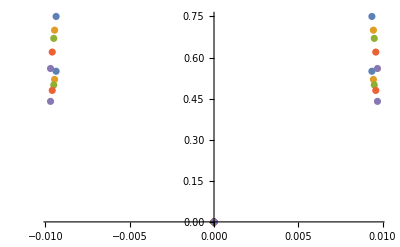

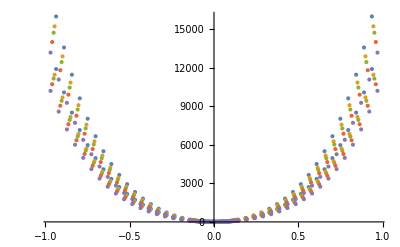

```mathematica
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;

(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,5}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,5}]

(*Zirconium*)
V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,5}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,5}]
```

```mathematica
V[1,2,x][[1]]
```

6264.46 x^2

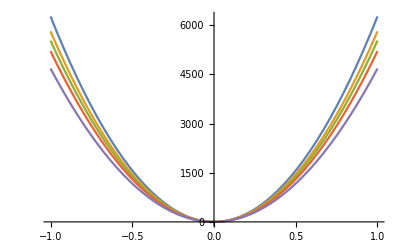

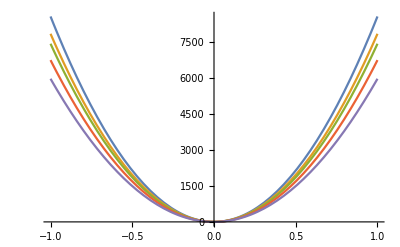

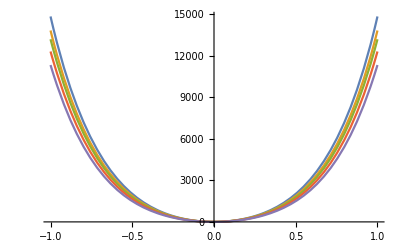

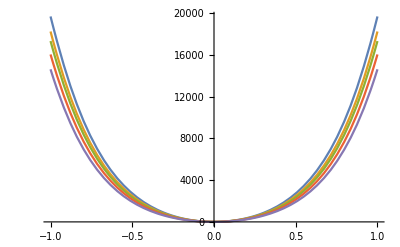

```mathematica
Plot[Evaluate@V[1,2,x],{x,-1,1}]
Plot[Evaluate@V[2,2,x],{x,-1,1}]
Plot[Evaluate@V[1,12,x],{x,-1,1}]
Plot[Evaluate@V[2,12,x],{x,-1,1}]
```

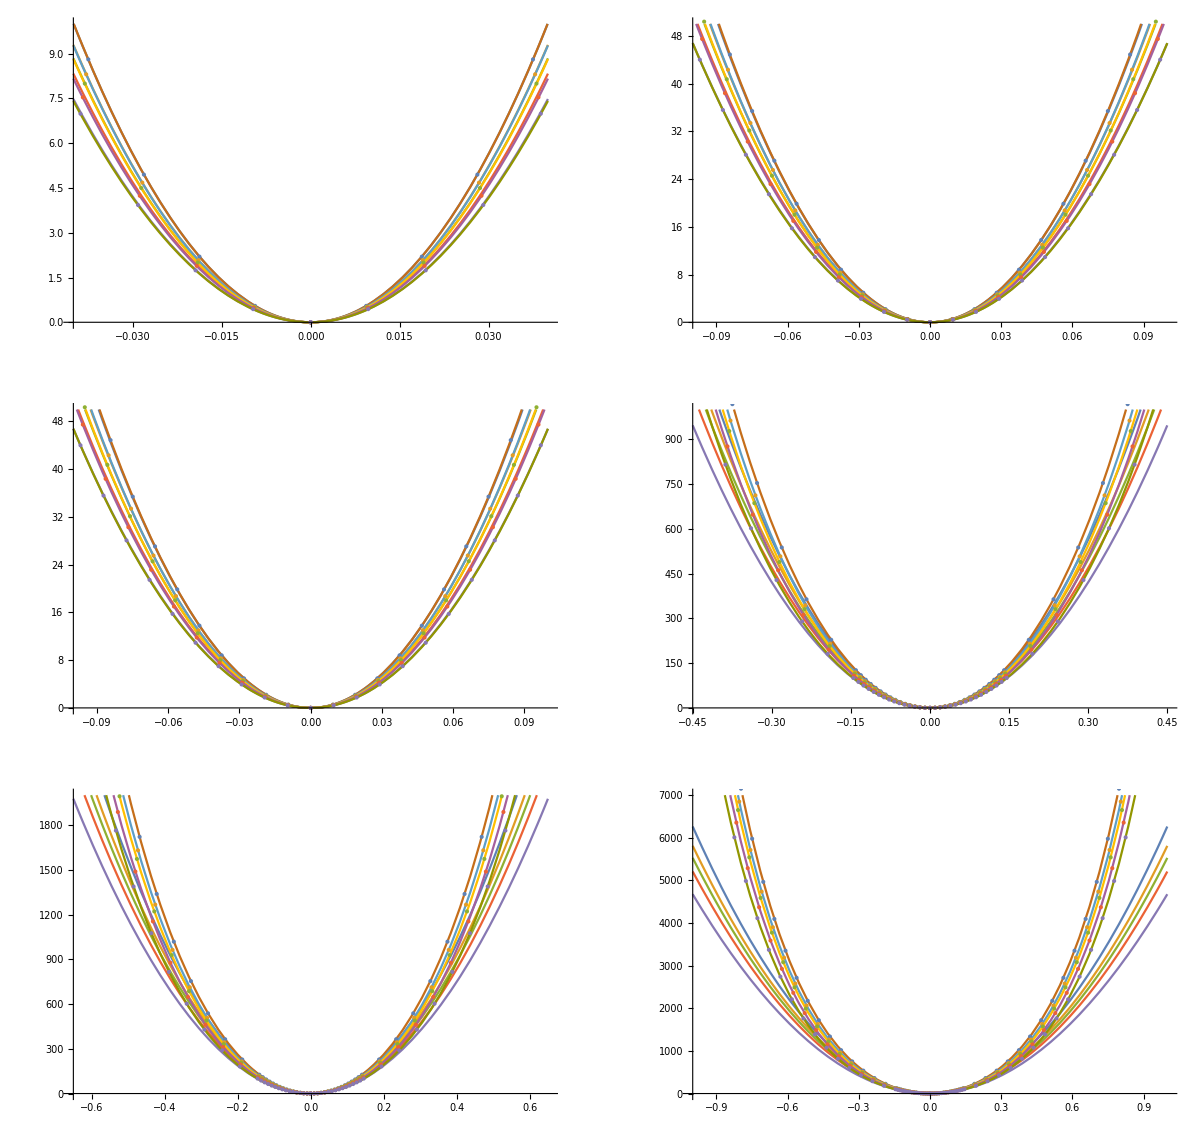

```mathematica
Carbon- look at the fits to examine agreement different length scales;
commonplotinfo={AxesLabel->{"Displacement (Å)","E-E0ref (meV) "}};
P00=With[{B=0.04,H=10},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2=With[{B=0.45,H=1000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3=With[{B=0.65,H=2000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4=With[{B=1,H=7000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00,ListPlot@Cdata],Show[P0,ListPlot@Cdata]},{Show[P1,ListPlot@Cdata],Show[P2,ListPlot@Cdata]},{Show[P3,ListPlot@Cdata],Show[P4,ListPlot@Cdata]}},ImageSize->1200]
```

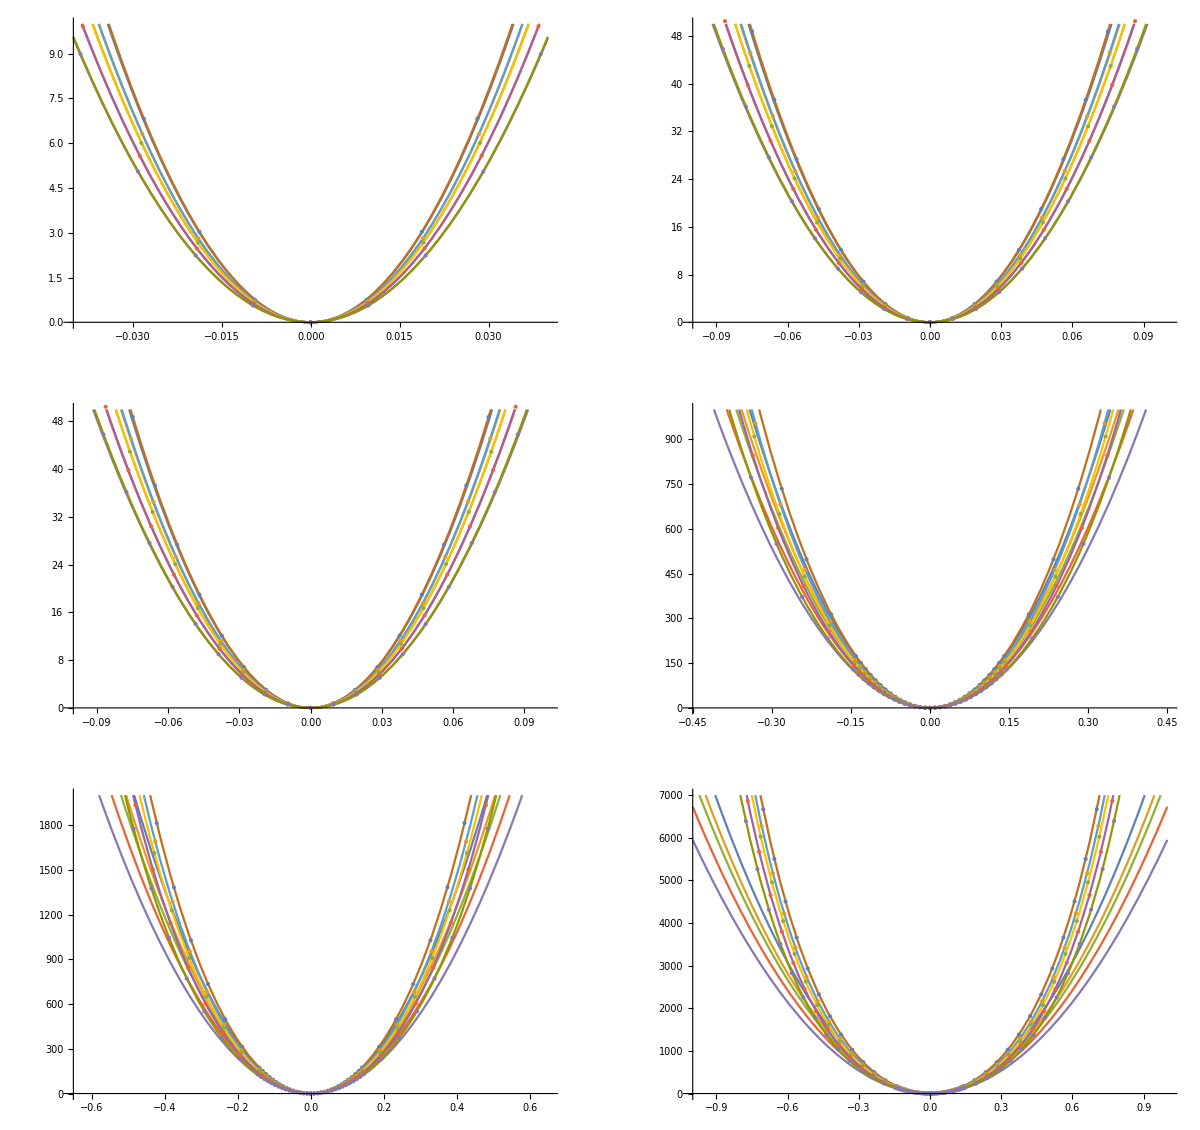

```mathematica
Look at fits at different scales - Zirconium;
P00z=With[{B=0.04,H=10},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2z=With[{B=0.45,H=1000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3z=With[{B=0.65,H=2000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4z=With[{B=1,H=7000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00z,ListPlot@Zrdata],Show[P0z,ListPlot@Zrdata]},{Show[P1z,ListPlot@Zrdata],Show[P2z,ListPlot@Zrdata]},{Show[P3z,ListPlot@Zrdata],Show[P4z,ListPlot@Zrdata]}},ImageSize->1200]
```

```mathematica
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`50."&);
```

```mathematica
Carbon and zirconium - calculate harmonic frequency of fit (as root of prefactor *2 over mass);
(*If the fitted carbon potential is f(x)=A*x*x, let it be equal to standard harmonic expression, f(x)=A*x*x=1/2*m*omega*omega*x*x*)
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,5}]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,5}]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{6264.46,5810.6,5528.52,5208.33,4676.37}

cOmega0 in meV/Ang**2/AMU is approximately

{32.2978,31.1058,30.3414,29.4497,27.9052}

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{8542.44,7821.96,7408.22,6727.43,5951.75}

Z_Omega_0 in meV/Ang**2/AMU is approximately

{13.6852,13.0954,12.7443,12.1447,11.4231}

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first 70 eigenvalues and eigenvectors*)
Neigenvalues=70;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒallc=Table[-(1/(2m[[1]]))*u''[x]+V[1,2i,x]*u[x],{i,1,6,5}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,2i,x]*u[x],{i,1,6,5}];
```

```mathematica
Carbon and zirconium eigensystem solution
(*ℒallc[[harmonic=1,anharmonic=2]][[volumes1,2,3,4,5]*)

(*harmonic eigensystems*)
(*Carbon eigensystem*)
eigensysCh=Table[NDEigensystem[ℒallc[[1]][[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,5}];
(*Zironcium eigensystem*)
eigensysZh=Table[NDEigensystem[ℒallz[[1]][[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,5}];

(*harmonic eigensystems*)
(*Carbon eigensystem*)
eigensysC=Table[NDEigensystem[ℒallc[[2]][[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,5}];
(*Zironcium eigensystem*)
eigensysZ=Table[NDEigensystem[ℒallz[[2]][[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,5}];
```

and Carbon eigensystem solution zirconium

```mathematica
(*eigensysCh[[vol]][[vals/vectors]]*)
(*Carbon harmonic and anharmonic spectrums*)

chrelspectrum=Table[(eigensysCh[[vol]][[1]]/eigensysCh[[vol]][[1]][[1]]-0.5)/(eigensysCh[[vol]][[1]]/eigensysCh[[vol]][[1]][[1]]-0.5),{vol,1,5}];
crelspectrum=Table[(eigensysC[[vol]][[1]]/eigensysC[[vol]][[1]][[1]]-0.5)/(eigensysCh[[vol]][[1]]/eigensysCh[[vol]][[1]][[1]]-0.5),{vol,1,5}];

cPrelspectrum=ListPlot[{chrelspectrum,
crelspectrum}];
(*Zr harmonic and anharmonic spectrums*)
zhrelspectrum=Table[(eigensysZh[[vol]][[1]]/eigensysZh[[vol]][[1]][[1]]-0.5)/(eigensysZh[[vol]][[1]]/eigensysZh[[vol]][[1]][[1]]-0.5),{vol,1,5}];
zrelspectrum=Table[(eigensysZ[[vol]][[1]]/eigensysZ[[vol]][[1]][[1]]-0.5)/(eigensysZh[[vol]][[1]]/eigensysZh[[vol]][[1]][[1]]-0.5),{vol,1,5}];
```

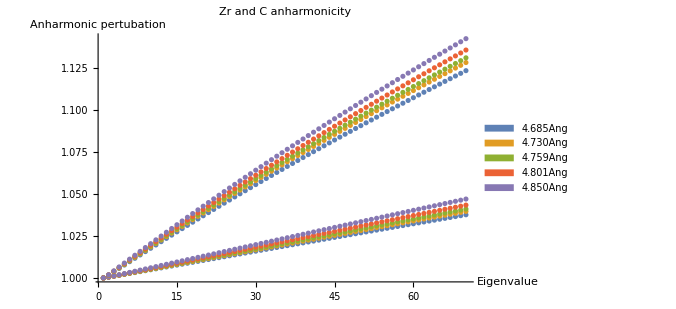

```mathematica
Show[ListPlot[zrelspectrum,PlotLegends->SwatchLegend[{"4.685Ang","4.730Ang","4.759Ang","4.801Ang","4.850Ang"}]],ListPlot[crelspectrum],PlotRange->All,PlotLabel->"Zr and C anharmonicity",AxesLabel->{"Eigenvalue","Anharmonic \npertubation"},ImageSize->500]
```

```mathematica
(*cabron anharmonic fits*)
(**)
anhfitz1=Table[Fit[zrelspectrum[[vol]],{1,x},x],{vol,1,5}]
anhfitz2=Table[Fit[zrelspectrum[[vol]],{1, x, x^2},x],{vol,1,5}]
anhfitz3=Table[Fit[zrelspectrum[[vol]],{1, x, x^2,x^3},x],{vol,1,5}]
anhfitz4=Table[Fit[zrelspectrum[[vol]],{1, x, x^2,x^3,x^4},x],{vol,1,5}]
(*Conclusion from different orders of fit to the anharmonic interaction shows quadratic wins*)
Show[Plot[{anhfitz1,anhfitz2},{x,1,140},PlotRange->All],ListPlot[zrelspectrum],ImageSize->1200];
Show[Plot[{anhfitz2,anhfitz3},{x,1,140},PlotRange->All],ListPlot[zrelspectrum],ImageSize->1200];
Show[Plot[{anhfitz2,anhfitz4},{x,1,140},PlotRange->All],ListPlot[zrelspectrum],ImageSize->1200];
```

{0.999464+0.000547792 x,0.999395+0.000577129 x,0.999363+0.000597659 x,0.999318+0.000631948 x,0.99927+0.000684489 x}

{0.999319+0.000559877 x-1.70206×10^-7 x^2,0.99928+0.000586703 x-1.34843×10^-7 x^2,0.999253+0.000606829 x-1.29164×10^-7 x^2,0.999208+0.00064106 x-1.28337×10^-7 x^2,0.99914+0.000695301 x-1.52287×10^-7 x^2}

{0.999344+0.000555712 x-2.45907×10^-8 x^2-1.36728×10^-9 x^3,0.999314+0.00058116 x+5.89447×10^-8 x^2-1.8196×10^-9 x^3,0.99929+0.000600699 x+8.51819×10^-8 x^2-2.01264×10^-9 x^3,0.999251+0.000634158 x+1.12993×10^-7 x^2-2.26601×10^-9 x^3,0.999187+0.00068759 x+1.17321×10^-7 x^2-2.53153×10^-9 x^3}

{0.999366+0.000550051 x+3.28254×10^-7 x^2-9.06088×10^-9 x^3+5.41803×10^-11 x^4,0.999337+0.000575045 x+4.40174×10^-7 x^2-1.01321×10^-8 x^3+5.85387×10^-11 x^4,0.999315+0.000594298 x+4.84163×10^-7 x^2-1.07122×10^-8 x^3+6.12646×10^-11 x^4,0.999276+0.000627307 x+5.4005×10^-7 x^2-1.15778×10^-8 x^3+6.55757×10^-11 x^4,0.999216+0.000680074 x+5.85863×10^-7 x^2-1.27478×10^-8 x^3+7.19458×10^-11 x^4}

```mathematica
(*Zr anharmonic fits*)
anhfitc1=Table[Fit[crelspectrum[[vol]],{1,x},x],{vol,1,5}]
anhfitc2=Table[Fit[crelspectrum[[vol]],{1, x, x^2},x],{vol,1,5}]
anhfitc3=Table[Fit[crelspectrum[[vol]],{1, x, x^2,x^3},x],{vol,1,5}]
anhfitc4=Table[Fit[crelspectrum[[vol]],{1, x, x^2,x^3,x^4},x],{vol,1,5}]

(*Linear vs quadratic fits to anharmonic perturbation*)
(*Conclusion from different orders of fit to the anharmonic interaction shows quadratic wins*)
Show[Plot[{anhfitc1,anhfitc2},{x,1,140},PlotRange->All],ListPlot[crelspectrum],ImageSize->1200];
```

{1.00059+0.00179198 x,1.00079+0.00186073 x,1.00076+0.00190162 x,1.0007+0.0019695 x,1.00068+0.00206821 x}

{0.99775+0.002029 x-3.33831×10^-6 x^2,0.997717+0.0021167 x-3.60522×10^-6 x^2,0.997661+0.0021597 x-3.63494×10^-6 x^2,0.99756+0.00223132 x-3.68759×10^-6 x^2,0.997417+0.00234028 x-3.83198×10^-6 x^2}

{0.997601+0.00205333 x-4.18881×10^-6 x^2+7.98594×10^-9 x^3,0.9975+0.00215213 x-4.84379×10^-6 x^2+1.16298×10^-8 x^3,0.997449+0.00219435 x-4.84631×10^-6 x^2+1.13744×10^-8 x^3,0.997363+0.00226348 x-4.81211×10^-6 x^2+1.05589×10^-8 x^3,0.997231+0.00237051 x-4.88863×10^-6 x^2+9.92158×10^-9 x^3}

{0.997656+0.00203894 x-3.29178×10^-6 x^2-1.15734×10^-8 x^3+1.37742×10^-10 x^4,0.997541+0.00214122 x-4.16374×10^-6 x^2-3.19832×10^-9 x^3+1.04423×10^-10 x^4,0.997493+0.00218262 x-4.11476×10^-6 x^2-4.57657×10^-9 x^3+1.12331×10^-10 x^4,0.997415+0.00224976 x-3.95649×10^-6 x^2-8.09743×10^-9 x^3+1.31383×10^-10 x^4,0.997293+0.00235423 x-3.87418×10^-6 x^2-1.2198×10^-8 x^3+1.55771×10^-10 x^4}

```mathematica
fanhc[x_]:=anhfitc2/.x->x
fanhz[x_]:=anhfitz2/.x->x
cOmega0
zOmega0
fanhcOmega[x_]:=anhfitc2*cOmega0/.x->x
fanhzOmega[x_]:=anhfitz2*zOmega0/.x->x
```

{32.2978,31.1058,30.3414,29.4497,27.9052}

{13.6852,13.0954,12.7443,12.1447,11.4231}

```mathematica
s0=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,10},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum]];
s1=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,50},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum]];
s2=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,200},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum]];
s3=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,300},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum,PlotLegends->SwatchLegend[{"4.685Ang","4.730Ang","4.759Ang","4.801Ang","4.850Ang"}]]];

GraphicsGrid[{{s0,s1,s2,s3}}]
```

-Graphics-

```mathematica
free[T_,spectrumZ_,spectrumC_,maxEigen_]:=-K2meV*1.5*T*Log[{Total[Exp[-2*Table[((0.5+x)*(spectrumZ)),{x,0,maxEigen}]/(K2meV*T)]],Total[Exp[-2*Table[((0.5+x)*(spectrumC)),{x,0,maxEigen}]/(K2meV*T)]]}]
```

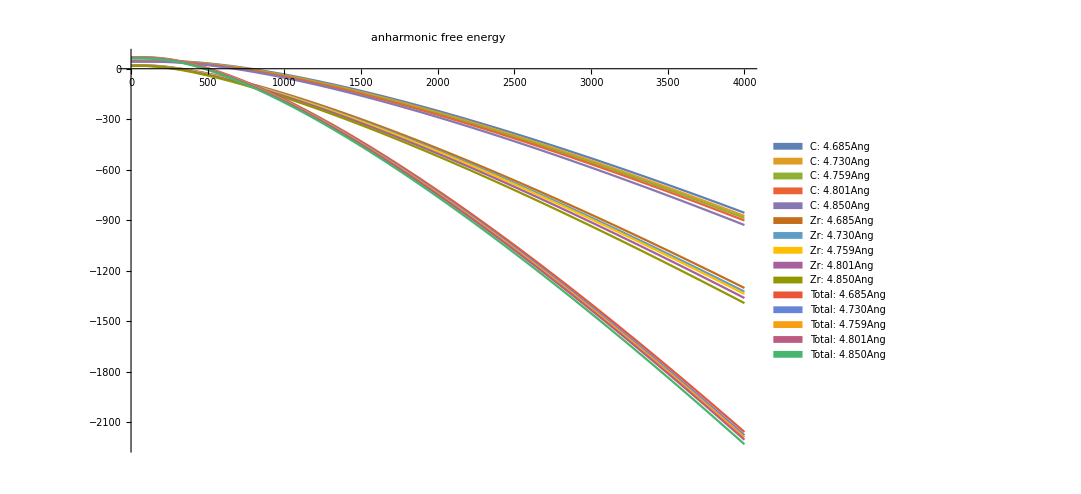

```mathematica
Plot[{Evaluate@(free[T,fanhcOmega[x],fanhzOmega[x],100]),Evaluate@Total@(free[T,fanhcOmega[x],fanhzOmega[x][[1]],100])}
,{T,1,4000},ImageSize->800,PlotLabel->"anharmonic free energy",PlotLegends->SwatchLegend[{"C: 4.685Ang","C: 4.730Ang","C: 4.759Ang","C: 4.801Ang","C: 4.850Ang","Zr: 4.685Ang","Zr: 4.730Ang","Zr: 4.759Ang","Zr: 4.801Ang","Zr: 4.850Ang","Total: 4.685Ang","Total: 4.730Ang","Total: 4.759Ang","Total: 4.801Ang","Total: 4.850Ang"}]]
```

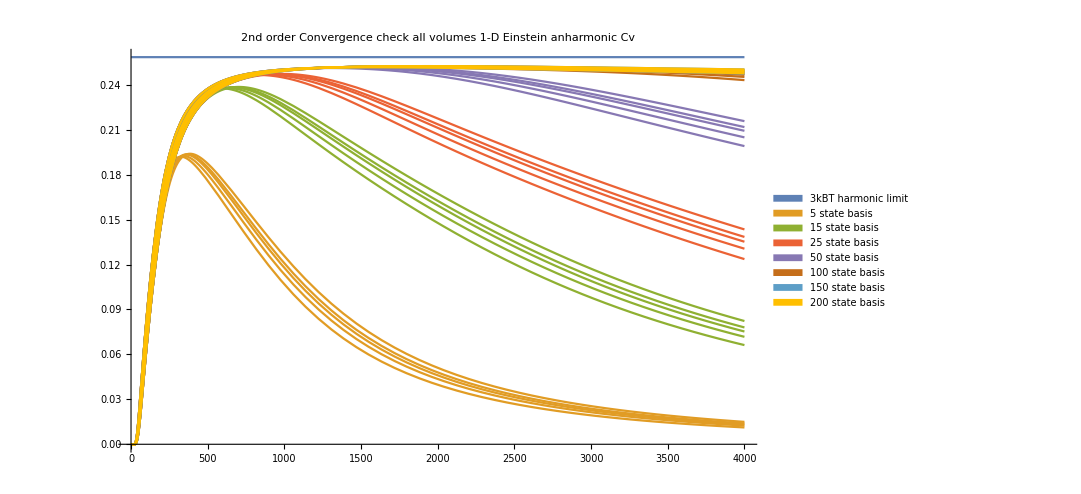

```mathematica
Plot[{K2meV*3,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],5],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],15],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],25],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],50],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],100],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],150],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],200],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800,PlotLabel->"2nd order Convergence check all volumes 1-D Einstein anharmonic Cv",PlotLegends->SwatchLegend[{"3kBT harmonic limit","5 state basis","15 state basis","25 state basis","50 state basis","100 state basis","150 state basis","200 state basis","300 state basis"}]]
```

```mathematica
(*All volumes anharmonic harmonic heat capcity comparison 30 basis*)
pha0=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],30],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,30],T],T]])/.T->t},{t,1,4000},PlotLabel->"30basis"];
(**PlotLegends->SwatchLegend[{"3kB","anharmonic 4.685Ang","anharmonic 4.730Ang","anharmonic 4.759Ang","anharmonic 4.801Ang","anharmonic 4.850Ang","harmonic 4.685Ang","harmonic 4.730Ang","harmonic 4.759Ang","harmonic 4.801Ang","harmonic 4.850Ang"}*)
(*All volumes anharmonic harmonic heat capcity comparison 100 basis*)
pha1=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],100],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,100],T],T]])/.T->t},{t,1,4000},PlotLabel->"100basis"];
(*All volumes anharmonic harmonic heat capcity comparison 200 basis*)
pha2=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],200],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,200],T],T]])/.T->t},{t,1,4000},PlotLabel->"200basis"];
(*(*All volumes anharmonic harmonic heat capcity comparison 300 basis - too big*)
pha3=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],300],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,300],T],T]])/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"3kB","anharmonic all volumes","harmonic all volumes"}],PlotLabel->"300basis"]*)
```

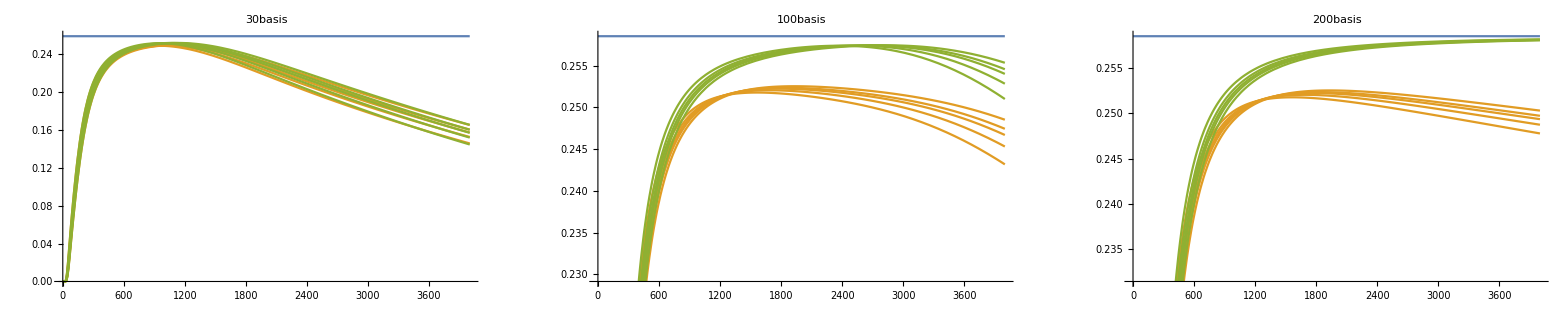

```mathematica
GraphicsGrid[{{pha0,pha1,pha2}},ImageSize->2500]
```

```mathematica
cvPerturb=(T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],200],T],T]-T*D[-D[free[T,cOmega0,zOmega0,200],T],T]);
```

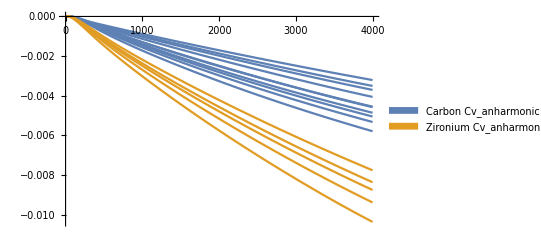

```mathematica
Plot[{Evaluate@cvPerturb/.T->t,Total[cvPerturb]/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"Carbon Cv_anharmonic","Zironium Cv_anharmonic","Total Cv_anharmonic"}]]
```

```mathematica
(*Import QHA dS/dV and dV/dT to convert Cv to Cp*)
```

```mathematica
temps={760,1900,2500,3200,3805};
anCv=Total[cvPerturb]/.T->temps
```

{{-0.00164725,-0.00402397,-0.00516352,-0.00641863,-0.00744413},{-0.00179504,-0.0043571,-0.00558259,-0.00692909,-0.00802569},{-0.00189079,-0.00457372,-0.00585496,-0.00726059,-0.00840276},{-0.00204665,-0.00492705,-0.00629863,-0.00779946,-0.00901335},{-0.0023029,-0.00549605,-0.00700684,-0.00865078,-0.00996733}}

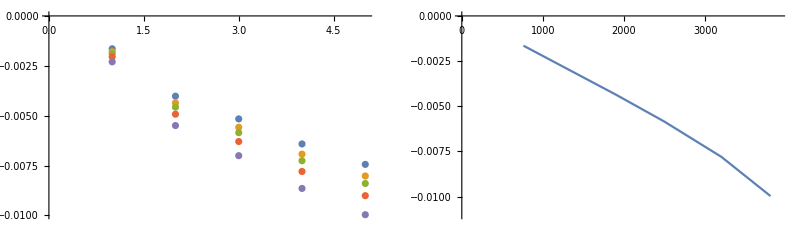

```mathematica
GraphicsGrid[{{ListPlot@anCv,ListPlot[Transpose@{temps,Table[anCv[[i]][[i]],{i,1,5}]},PlotRange->{{0,3900},{-0.011,0}},Joined->True]}},ImageSize->800]
```

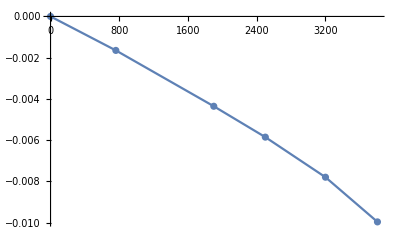

-0.0000512869-1.87489×10^-6 T-1.85187×10^-10 T^2

```mathematica
anCvdata=Partition[Flatten@{{0,0},Transpose[{temps,Table[anCv[[i]][[i]],{i,1,5}]}]},2];
Show[ListPlot[anCvdata],ListPlot[anCvdata,Joined->True]]
Cvanfit=Fit[anCvdata,{1,T,T^2},T]
```

```mathematica
(*Cp=Cv+T*dV/dT*dS/dV*)
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
qhaNormal={"QHA_normal/e-v.dat","QHA_normal/volume_expansion.dat","QHA_normal/volume-temperature.dat","QHA_normal/gruneisen-temperature.dat","QHA_normal/gibbs-temperature.dat","QHA_normal/bulk_modulus-temperature.dat","QHA_normal/Cp-temperature.dat","QHA_normal/dsdv-temperature.dat"};
normal=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,1,8}];
```

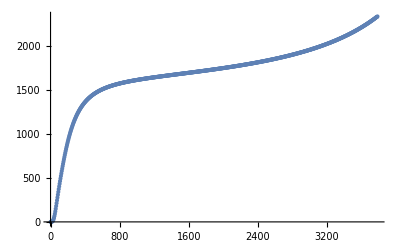

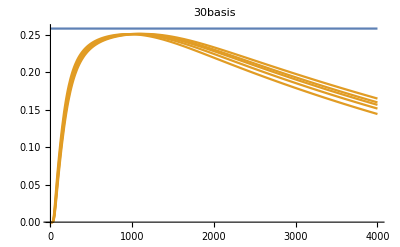

```mathematica
ListPlot[normal[[7]]]
Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,30],T],T]])/.T->t},{t,1,4000},PlotLabel->"30basis"]
```

```mathematica
kjmol2evatom=1/(96.487*64);
qhaCpeVatom=Transpose[{Transpose[normal[[7]]][[1]],Transpose[normal[[7]]][[2]]*kjmol2evatom}];
interQhaCp[T_]:=Interpolation[qhaCpeVatom][T]
```

```mathematica
harmCv[T_]:=1.5*(K2meV*((((2cOmega0[[1]]))/(K2meV*T))^2)*Exp[((2cOmega0[[1]]))/(K2meV*T)]/((Exp[((2cOmega0[[1]]))/(K2meV*T)]-1)^2)+K2meV*((((2zOmega0[[1]]))/(K2meV*T))^2)*Exp[((2zOmega0[[1]]))/(K2meV*T)]/((Exp[((2zOmega0[[1]]))/(K2meV*T)]-1)^2))
```

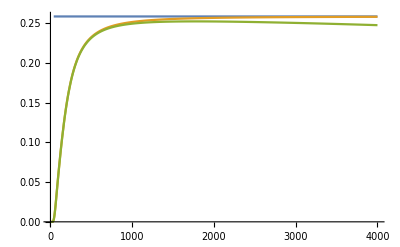

```mathematica
Plot[{3K2meV,harmCv[T],harmCv[T]+Cvanfit/.T->T},{T,1,4000},PlotRange->All]
```

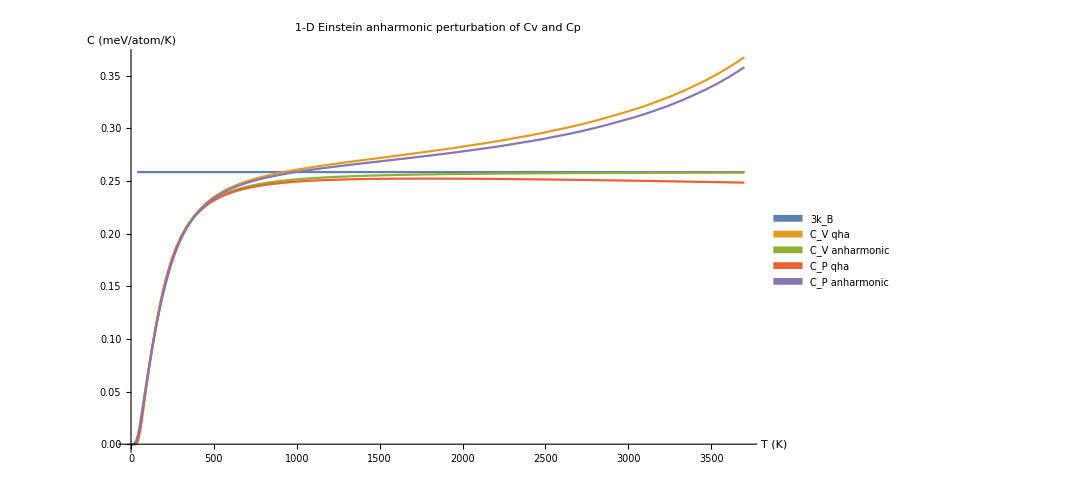

```mathematica
(*Plot the volume dependent anharmonic pertubuation of Cv and Cp*)
Plot[{3K2meV,interQhaCp[T],harmCv[T],harmCv[T]+Cvanfit/.T->T,interQhaCp[T]+Cvanfit/.T->T},{T,1,3700},PlotRange->All,PlotLabel->"1-D Einstein anharmonic perturbation of Cv and Cp",PlotLegends->SwatchLegend[{"3k_B","C_V qha","C_V anharmonic","C_P qha","C_P anharmonic"}],ImageSize->800,AxesLabel->{"T (K)","C (meV/atom/K)"}]
```

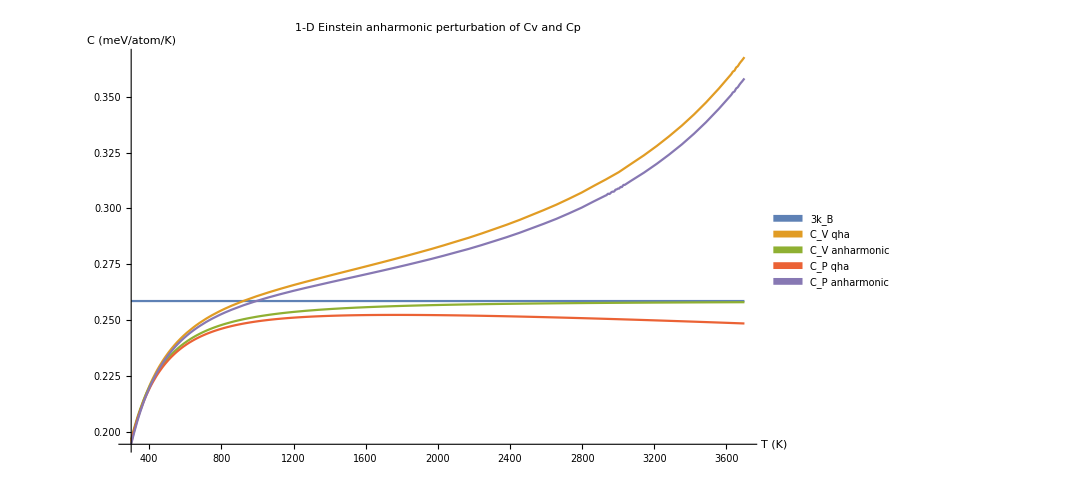

```mathematica
(*Plot the volume dependent anharmonic pertubuation of Cv and Cp*)
Plot[{3K2meV,interQhaCp[T],harmCv[T],harmCv[T]+Cvanfit/.T->T,interQhaCp[T]+Cvanfit/.T->T},{T,300,3700},PlotRange->All,PlotLabel->"1-D Einstein anharmonic perturbation of Cv and Cp",PlotLegends->SwatchLegend[{"3k_B","C_V qha","C_V anharmonic","C_P qha","C_P anharmonic"}],ImageSize->800,AxesLabel->{"T (K)","C (meV/atom/K)"}]
```

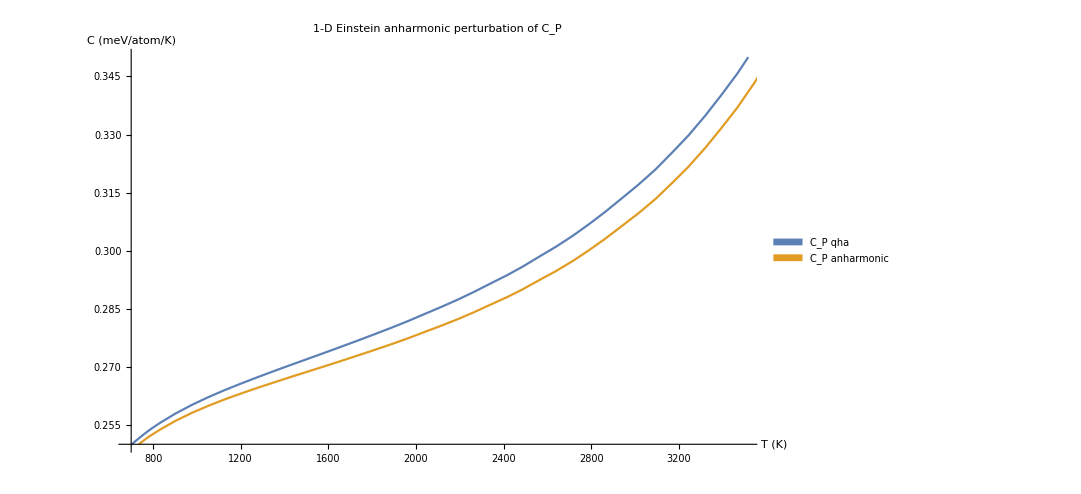

```mathematica
(*Plot the volume dependent anharmonic pertubuation of Cv and Cp*)
Plot[{interQhaCp[T],interQhaCp[T]+Cvanfit/.T->T},{T,1,3700},PlotLabel->"1-D Einstein anharmonic perturbation of C_P",PlotLegends->SwatchLegend[{"C_P qha","C_P anharmonic"}],ImageSize->800,AxesLabel->{"T (K)","C (meV/atom/K)"},PlotRange->{{700,3500},{0.25,0.35}}]
```